## Definition of the Derivative

### Main definition of the Derivative

We have calculated the slope of a tangent line with the limit:

```mathematica
m=lim_(h->0) (f(x+h)-f(x))/h
```

In calculus, this special limit is called the Definition of the Derivative and has special notation. Instead of “m”, we typically use:

```mathematica
f' (x) = lim_(h->0) (f(x+h)-f(x))/h
```

The derivative is a function related to f(x) that will tell you the instantaneous rate of change of f(x) or the slope of a tangent line to f(x) at any point along the curve. 
There are several different notations:

```mathematica
f'(x), y', f', dy/dx, ⅆ/ⅆx(f(x))
```

Basically, if you are working with a function named f(x), then you will probably use f'(x) for the derivative. If you are working with a function defined as y=…, then you will probably use y' or dy/dx.

Type your favorite derivative notation (from the list above) in the text cell:

Now type the same thing into the input cell and then press the [shift] and [enter] keys together to evaluate

The Wolfram Language (WL) just echoed your input since we have not defined a function.

### Alternate Definitions of the Derivative

Using the points (x, f(x) ) and (a, f(a) ) and our Algebra 1 slope definition, leads to the following derivative:

```mathematica
f'(x)=lim_(x->a) (f(x)-f(a))/(x-a)
```

This definition is extremely handy when finding f'(2) or f'(-7), but not f'(x).

Define f(x)=x^3 in the next input cell. Click in the cell and press [shift] and [enter] together:

```mathematica
f[x_]:=x^3
```

Note that Mathematica (WL) needs square brackets (not parenthesis) and when defining functions, we will use “x_” on the left side and “:=” instead of a regular equal sign More on this later.

Insert graph with tangent line and grid to calculate the slope

Calculate f'(2), the slope of the tangent line to f(x) at x=2, by typing f'[2] in the following input cell (don’t forget to hit [shift] [enter] to evaluate):

```mathematica
f'[2]
```

This number is the slope of the tangent line to f(x)=x^3 at x=2.

Now that you know the answer for f'(2), the derivative of x^3 at x=2, let’s use the Alternate Definition of the Derivative to prove that our answer is correct.

f'(a)=lim _(x→a) (f(x)-f(a))/(x-a)
f'(2)=lim _(x→2) (f(x)-f(2))/(x-2)
=lim _(x→2) (x^3-8)/(x-2)
=lim _(x→2) ((x-2)(x^2+2x+4))/(x-2)
=lim _(x→2) (x^2+2x+4)    parenthesis needed!
=4+4+4
f'(2)=12

This is the answer from above...but without a calculator or computer. 
Correct notation is very important!

### Finding Derivatives on the TI-84

Your TI-84 will not find f'(x), but it will find f'(2) and has surprisingly good notation for finding derivatives at

Your TI-84 is not doing calculus like Mathematica does. In fact, it uses two points very close to each other and calculates Algebra 1 slope. Sometimes on a test you might see one of the following limits, which are different versions of the Definition of the Derivative, but using slightly different starting points.

Using (x+h, f(x+h) ) and (x-h,f(x-h) ):

```mathematica
f'(x)=lim_(h->0) (f(x+h)-f(x-h))/(2h)
```

Using (x, f(x) ) and (x-h,f(x-h) ):

```mathematica
f'(x)=lim_(h->0) (f(x)-f(x-h))/h
```

#### The Bottom Line:

When you have to use the Definition of the Derivative:

To find f'(x), then use f' (x) = lim_(h→0) (f(x+h)-f(x))/h
To find f'(a), a = any constant, then use f'(x)=lim_(x→a) (f(x)-f(a))/(x-a)

Use the Definition of the Derivative to find g'(-3) for g(x)=5 x^2:

## Differentiability

A function is differentiable if you can find the derivative at any point in its domain. Often it is helpful to picture the graph of a function to determine if it is differentiable...able to take the derivative...able to find the slope of a tangent line at any point.

Most of the functions that we will study in calculus will be differentiable, but some might have one or more points where the function is not differentiable. If a function is NOT differentiable at a point (a,f(a) ), then:

```mathematica
lim_(x->a) (f(x)-f(a))/(x-a)=DNE
```

You might describe this to a friend as: “At x=a, you cannot calculate the slope of a tangent line to f(x).

To be differentiable, a function must be continuous and smooth, without vertical tangent lines.

The following four functions are Not differentiable at x=0.
y=|x|,  y=x^(2/3),  y=x^(1/3),  y=(|x|)/x

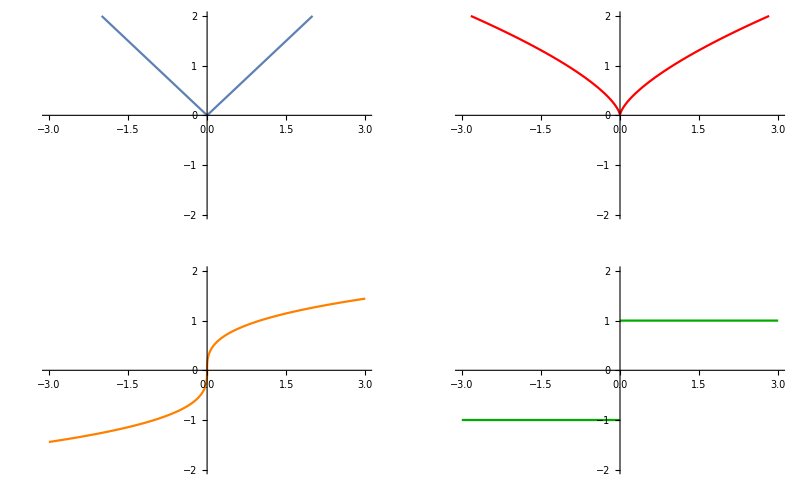

```mathematica
p1=Plot[Abs[x],{x,-3,3},PlotRange->{-2,2}];
p2=Plot[(x^2)^(1/3),{x,-3,3},PlotRange->{-2,2},PlotStyle->Red];
p3=Plot[CubeRoot[x],{x,-3,3},PlotRange->{-2,2},PlotStyle->Orange];
p4=Plot[Abs[x]/x,{x,-3,3},PlotRange->{-2,2},PlotStyle->Darker[Green]];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```

Explain why each graph above is not differentiable at x=0:

### Differentiability Theorems

#### If f(x) has a derivative at x=a, then f(x) is continuous at x=a.

One of the following is true:

If f(x) does not have a derivative at x=a, then f(x) is not continuous at x=a.
If f(x) is continuous at x=a, then f(x) is is differentiable at x=a.
If f(x) is not continuous at x=a, then f(x) is is not differentiable at x=a.

Which one is true? What are counterexamples for the other two?

Insert Manipulate to slide to make a sharp point and ask what value makes this not differentiable?

#### Intermediate Value Theorem for Derivatives

If a and b are any two points in an interval where f(x) is differentiable, then f'(x) takes on every value between f'(a) and f'(b).

## Local Linearity

Use the slider to zoom in:

```mathematica
g[x_]:=(0.5x)Sin[x];
Manipulate[
Plot[g[x],{x,2.5-zoom,2.5+zoom},PlotRange->{g[2.5]-.8zoom,g[2.5]+.2zoom},PlotLabel->"y=f(x)"],
{zoom,3,.01,-.01},SaveDefinitions->True]
```

What does the graph look like when you zoom in?

### Linear Approximation

Mouse on ping pong ball, basketball, hot air balloon, person on earth...at what point...

It is often useful to use a line near a point of tangency to approximate a function value. For example, here is what a quiz question might look like:

For g(x)=3 x^2, estimate g(-1.01) using a tangent line approximation at x=-1.

The steps to solve this problem are:
1. Find the equation of the tangent line to g(x) at x=-1.
	a. Find the point
	b. Find the slope
	c. Write the equation of the tangent line.
2. Substitute x=-1.01 into the tangent line equation and solve for y.

Here is the solution:
1.	Point:  g(-1)=3, so the point is (-1,3).
	Slope: g'(x)=6x
		g'(-1)=-6, so the slope is -6. 
	Tangent line equation (point-slope form): y-3=-6(x+1).
2. Substitute x=-1.01 into the tangent line equation and solve for y:

y-3=-6(-1.01+1)
y=-6(-0.01)+3
y=0.06+3
y=3.06
g(-1.01)=3.06

#### Now you try:

For f(x)=5-1/3 x^3, estimate f(2.99) using a tangent line approximation at x=3.

## Authorship Information

Dan Uhlman
uhlmand@tas.tw